creatingintelligence.org

```mathematica
Module[{LEFTMARGIN=62,FONT="Inter Variable",TITLECOLOR=RGBColor["#BF616A"],TEXTCOLOR=RGBColor["#2E3440"]},(*Change LEFTMARGIN to whatever pixel/point value centers the 600px content*)SetOptions[EvaluationNotebook[],DockedCells->{Cell[BoxData[ToBoxes[Row[{Button["Export",Module[{nb=EvaluationNotebook[],cleanPath},cleanPath=FileNameJoin[{NotebookDirectory[nb],FileBaseName[NotebookFileName[nb]]}];
Export[cleanPath<>".pdf",nb];
Export[cleanPath<>".json",DATAFLOW, "Circuit"]],Method->"Queued"]}]]],"DockedCell",Background->RGBColor["#EBCB8B"],CellMargins->{{0,0},{0,0}}]},(*Headers and Footers*)

PageHeaders->{{"","",""},{"","",""}},

PageFooters->{{"",Cell[TextData[CounterBox["Page"]]],""},{"",Cell[TextData[CounterBox["Page"]]],""}},

PageFooters->{{"",Cell[TextData[CounterBox["Page"]]],""},{"",Cell[TextData[CounterBox["Page"]]],""}},


PrintingOptions->{"PaperSize"->{510,680},(*{width,height} for Portrait*)"PrintingMargins"->{{0,0},{30,30}} (*left/right,bottom/top margins*)},(*Stylesheet overrides*)

StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],(*No header/footer lines*)
Cell[StyleData["Header","Printout"],CellFrame->0],Cell[StyleData["Footer","Printout"],CellFrame->0],Cell[StyleData["Title","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{10,0}}],

Cell[StyleData["Subtitle","Printout"],FontColor->TITLECOLOR,FontSize->20,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{20,0}}],

Cell[StyleData["Section","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellFrame->False,PageBreakAbove->True,GroupPageBreakWithin->True,CellMargins->{{LEFTMARGIN,0},{20,10}}],Cell[StyleData["Subsection","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{10,10}}],Cell[StyleData["Subsubsection","Printout"],FontColor->TITLECOLOR,FontFamily->FONT,CellMargins->{{LEFTMARGIN,0},{10,10}}],Cell[StyleData["Text","Printout"],Hyphenation->True,
LineSpacing -> {1.4,0},FontColor->TEXTCOLOR,FontFamily->FONT,CellFrame->False,CellMargins->{{LEFTMARGIN,60},{7,7}}],Cell[StyleData["Code","Printout"],CellFrameMargins->{{20,0},{8,8}},PageWidth->670,CellMargins->{{LEFTMARGIN,30},{7,15}}],
    Cell[StyleData["Program"], 
			CellOpen -> True, 
			FontFamily -> "JetBrains Mono",
			FontSize-> 10,FontColor -> Black,
			ShowCellBracket -> False, 
			CellMargins -> {{LEFTMARGIN, 0}, {-2, -2}},
			CellElementSpacings -> {"CellMinHeight" -> 0, "ClosedCellHeight" -> 0},
			CellFrame -> 0,CellFrameMargins -> 0,Background -> None
			],

Cell[StyleData["Output","Printout"],PageWidth->660,CellMargins->{{LEFTMARGIN+20,0},{10,10}}],(*Hide Input cells in Printout*)Cell[StyleData["Input","Printout"],CellOpen->False,ShowCellBracket->False,CellMargins->{{LEFTMARGIN,0},{-2,-2}},CellElementSpacings->{"ClosedCellHeight"->0}]}]]];


json := DATAFLOW = ImportString[ First[FrontEndExecute[FrontEnd`ExportPacket[
	NotebookRead[PreviousCell[]],"PlainText"]]], "Circuit"]
```

# Semantic Similarity Index

## Measuring the similarity of semantic fields with ARI

Store a dataset of circa 1.8M word associations (e.g. “ship”->”sail”) in hetero-associative memory. Retrieve the activation map for multiple words. Measure their similarity via the Adjusted Rand Index.

### Requirements

```mathematica
<< "Circuits.m"
```

### Circuit

{
  "$schema": "https://creatingintelligence.org/schemas/circuit-v1.json",

  "hyperparameters": {"default": [5000, 10]},

  "dataflow": [
	{"component": "input", "plugin": "codec", "send": [1]},

	{"component": "input", "plugin": "codec", "send": [2]},

	{"component": "associator", "send": [11], "receive": [2, 1]},

	{"component": "output", "receive": [11]}
  ]
}

```mathematica
circ = Circuit[json]; 
f = circ["function"];
circ["schematics"][ImageSize->220]
```

-Graphics-

### Import dataset

```mathematica
data = Import[ NotebookDirectory[] <>  "/data/word-associations.csv.zip", 
          "word-associations.csv"];
```

```mathematica
RandomSample[data, 10]
```

{{centralism,system},{solutions,replacement},{appraised,performance},{dispersant,clean-up},{lede,beginning},{waterlogged,soil},{antimatter,symmetry},{squalidness,wretchedness},{hundred,cent},{lapses,missteps}}

```mathematica
Length[data]
```

1888505

### Train

```mathematica
f @@@ data;
```

### Adjusted Rand Index

```mathematica
ARI[A_List, B_List, dim_Integer] := 
	N[(Length[Intersection[A,B]] - Length[A]*Length[B] / dim ) /
			(Min[Length[A], Length[B]] -  Length[A]*Length[B] / dim)]
```

```mathematica
similarity[x_, y_] := ARI[ f[x, Null], f[y, Null], 5000]
```

### Test

Retrieve activation map.

```mathematica
f["cat", Null]
```

Sequence[{9,12,25,29,41,49,65,68,69,70,72,90,124,126,131,141,154,165,174,179,181,183,194,209,219,223,226,233,237,249,257,272,277,286,287,300,301,318,334,341,346,362,368,374,381,387,410,416,431,451,452,457,458,462,463,466,476,479,507,509,517,518,519,534,538,539,540,544,552,563,570,603,604,610,618,630,645,649,664,668,674,687,702,710,730,743,756,758,768,793,800,833,835,841,855,863,881,897,898,901,902,904,906,909,916,923,932,934,946,948,966,975,981,983,985,991,995,1000,1003,1008,1019,1033,1040,1043,1045,1054,1055,1066,1068,1109,1118,1131,1132,1134,1166,1168,1169,1174,1185,1186,1188,1206,1222,1249,1286,1289,1294,1350,1354,1355,1356,1361,1363,1377,1387,1389,1412,1419,1438,1481,1482,1504,1516,1526,1533,1537,1547,1553,1568,1592,1601,1625,1626,1634,1637,1641,1642,1643,1666,1683,1700,1716,1758,1773,1796,1812,1821,1824,1826,1830,1842,1847,1861,1863,1869,1874,1887,1890,1891,1892,1911,1926,1929,1945,1949,1985,2019,2034,2088,2089,2091,2094,2124,2135,2142,2144,2151,2167,2172,2177,2195,2200,2210,2211,2214,2215,2238,2242,2244,2247,2264,2290,2292,2308,2329,2348,2354,2367,2370,2380,2394,2410,2419,2427,2428,2431,2432,2434,2450,2470,2473,2489,2492,2512,2532,2533,2547,2550,2565,2576,2607,2612,2617,2637,2641,2651,2660,2663,2666,2668,2670,2682,2684,2686,2688,2692,2710,2715,2721,2740,2746,2750,2751,2754,2764,2769,2770,2788,2793,2797,2801,2814,2824,2831,2851,2892,2901,2904,2908,2921,2928,2929,2930,2931,2932,2937,2942,2954,2977,2999,3000,3016,3039,3042,3053,3064,3074,3077,3084,3092,3097,3121,3124,3129,3130,3136,3137,3147,3152,3154,3155,3160,3177,3196,3200,3211,3235,3257,3258,3264,3271,3280,3289,3302,3310,3311,3318,3321,3332,3337,3354,3356,3361,3373,3374,3380,3383,3388,3398,3411,3453,3473,3503,3504,3513,3530,3532,3537,3549,3577,3579,3593,3612,3636,3637,3644,3652,3662,3664,3682,3694,3698,3708,3713,3714,3718,3720,3736,3756,3760,3761,3763,3774,3813,3837,3838,3843,3854,3864,3870,3873,3875,3883,3902,3903,3915,3923,3938,3943,3965,3972,3982,3985,3994,4044,4050,4070,4072,4076,4086,4104,4106,4123,4143,4159,4165,4170,4190,4197,4200,4220,4232,4234,4244,4266,4271,4279,4288,4298,4301,4308,4315,4322,4323,4326,4341,4347,4357,4358,4366,4368,4379,4394,4401,4403,4407,4408,4412,4418,4427,4455,4459,4476,4510,4511,4515,4519,4538,4541,4548,4557,4560,4571,4574,4583,4594,4603,4609,4610,4618,4626,4635,4648,4651,4663,4680,4686,4699,4709,4714,4722,4726,4740,4742,4744,4747,4757,4759,4768,4779,4787,4819,4823,4830,4844,4845,4866,4884,4892,4894,4896,4907,4919,4927,4942,4949,4967,4974,4986,4996,4998}]

Measure semantic similarity via ARI:

```mathematica
similarity["ship", "boat"]
```

0.633625

```mathematica
similarity["ship", "cheese"]
```

-0.00990518

### Similarity Matrix

```mathematica
SimilarityMatrix[ items_List] := Module[ {simtable, xTicks, yTicks},
	
	simtable = Outer[ Round[similarity[##], 0.001]&, items, items]; 
	xTicks=Table[{i,Rotate[items[[i]],90 Degree], {0,0}},{i,Length[items]}];
	yTicks=Table[{i,items[[i]], {0,0}},{i,Length[items]}];
	
	MatrixPlot[simtable, 
		FrameTicks -> {{yTicks, None}, {None, xTicks}},
		FrameStyle -> Opacity[0],
		FrameTicksStyle -> Directive[Opacity[1],
		FontFamily -> "Inter Variable",
		FontSize->12]]
	]
```

```mathematica
items = {"cat",  "dog", "lion", "piano", 
      "electric", "power", "king", "queen", "liberty"};
```

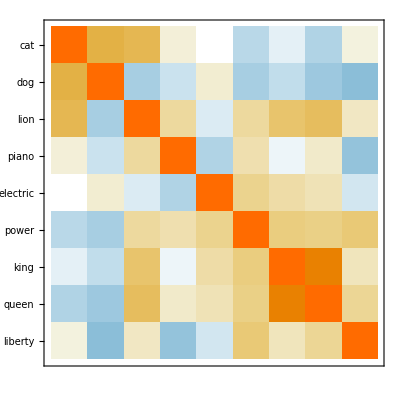

```mathematica
SimilarityMatrix[ items]
```

```mathematica
(* Export["similaritymatrix.png", ImagePad[Rasterize[%], 30, White]]; *)
```